## Voltage Dividers and Capacitors

## Analog Electronics, 2026-01-30

## THIS VERSION OF THE 2026-01-30 HANDOUT WAS WORDSMITHED AFTER CLASS. Capacitance is an extremely important subject, and probably it deserves a handout just titled “Capacitance,” but in this handout I am going to start with voltage dividers and soon you’ll see why they are closely related. A “voltage divider” is another way to think about resistors in series.

## Resistors in Series

Recall from the previous handout, our analysis of this circuit:

We learned that R_1 and R_2 connected in series act exactly like a resistor with size R_1+R_2. What does that mean!? It means that the current through a combination of two resistors also obeys Ohm’s Law, but with the constant of proportionality being R_1+R_2.

V_0=I(R_1+R_2)

Solving for I, 

I=V_0/(R_1+R_2)

As an example, if V_0=6V, with R_1=1kΩ and R_2=3kΩ, what is I? Answer conveniently in mA.

## Voltage Dividers

A key formula from the previous section was

I=V_0/(R_1+R_2)

Think about the resistor R_2. We usually declare the minus side of the battery to be at 0V, so that means the lower connector of R_2 is at 0V.

What voltage is the upper connector of R_2 at (the one that connects R_2 to R_1)?

I’m going to leave that for you to figure out rather than writing it up. You have the tools! Once you have figured it out, you’ll see why it is called a voltage divider.

Using the example from the previous section to plug in values. What is the voltage on the upper connector of R_2?

## Capacitors — But First Batteries

When I introduced charge, I hope I convinced you that charge can never pile up. And indeed it cannot!! Except there is one exception, that uses a loophole in the language. It is a specially-designed device that kind of allows charge to pile up.

Let’s revisit batteries. A battery can emit current for quite a while. In fact, the batteries we are using are spec’d to emit 3000mAh in total, which we did a bit of math and discovered was 10,800 Coulombs. Does a battery have 10,800 Coulombs piled up in it?

Seminar on that.

That will get you wondering what even is a battery!

BTW, I paid $12 for that image and I am required to give credit, and it is good to do that anyway, even if it isn’t required. It is by ser_igor, and is available on istockphoto.com https://www.istockphoto.com/vector/li-ion-battery-diagram-gm825367806-133778177.

I have zero clue (well, not quite zero) what is being shown. What I do know is that when you package this kind of chemistry into a battery you can by, electrons really want to come out of the end of the battery that is flat and go into the end with the button. By “really want” I mean that when one electron with charge -1.6 x10^-19 C leaves the flat (minus) end, it “falls upward” through 1.6V of potential through the circuit to the button (plus) end, and in doing so, 1.6 10^-19 C × 1.6V=2.56 10^-19 J of energy is available to be used by the circuit.

What if 3mA of current runs out of the battery for 10 minutes? How many Joules is that? Remember our 102g tangerine? How high could a motor using that amount of energy lift that tangerine? Assume (for simplicity) perfect efficiency, which is bogus, but still, it is a good calculation, and feel free to put in a factor of 0.3 for 30% efficiency if you want to make it more realistic.

The only difference between a capacitor and a battery is that a capacitor can be charged and discharged essentially an infinite number of times. Some capacitors have finite lifetimes due to the chemicals in them eventually decaying, but the lifetimes are measured in many years, and you might charge and discharge them thousands of times per second for all those years, which would be something like 10^11 charges and discharges.

So why don’t we use capacitors instead of batteries?!?

## Capacitance

A capacitor is a circuit element that obeys this law (which like Ohm’s Law is not a law):

v=q/C

Notice that we have an italic V and an italic C in that equation. And I am not going to go insert Gothic script characters anymore to help you distinguish, V and C from V and C. Sorry, there is only so much typesetting and word-smithing I can realistically do, and the italics key-combination is so much handier than bringing up a Gothic script palette.

The V in the formula is the voltage of the capacitor. The q is how much charge the capacitor is holding. C is a property of the capacitor design called the capacitance. 

When we say the capacitor is “charged” or there capacitor is “holding charge,” there is a loophole in the language. The capacitor is always holding net zero charge inside of it. What “charged” means is that the capcitor has q of charge connected to one terminal and -q of charge connected to the other terminal, and the q of charge really wants to go through the circuit and combine with the -q and when it is allowed to, the capacitor will be “discharged, ” just like a battery.

Here is the simplest circuit that can charge a capacitor:

## The Unit of Capacitance

Look at the “law” that applies to capacitors:

v=q/C

Notice that the proportionality constant C is in the denominator (and is italicized to distinguish it from C, the abbreviation for the Coulomb unit). This is unlike Ohm’s Law  (V=IR), where the proportionality constant R is in the numerator when you solve for V. You can rearrange the capacitance formula to get the C in the numerator:

q=CV

The way to think about that, when comparing capacitors with different capacitances, is to say that for a given voltage, the bigger capacitor will hold more charge.

AGAIN, REMEMBER, WE ARE USING A LOOPHOLE IN THE LANGUAGE when we say “charged” or “holds charge.” A capacitor is always net neutral, like any circuit element. But it has charge within it that really wants to go from one connector through the circuit and get to the other connector where it can combine with the opposite charge that is waiting there.

Rearrange yet again, but this time solve for C:

C=q/V

The right-hand side (RHS) has units of Coulomb/Volt. I can tell you, without you having to back through all the previous handouts, that we have never had that combination!

And that combination is going to come up so often when dealing with capacitors that for convenience we could really use a name for it. It is the Farad (abbreviated F), named after Michael Faraday:

1F=(1C)/(1V)

Faraday is the guy that discovered the properties of coils of wire that allowed Westinghouse to design the generators and motors that Nunn first used in mining in Utah.

## Charging the Capacitor

If you have had a bunch of calculus, it is pretty easy to analyze the RC circuit. I am not assuming calculus in this course, so we will use a non-calculus approach called “numerical analysis.” Even if you know calculus, numerical analysis provides a useful way to think about RC circuits.

Suppose the RC circuit previously drawn has been connected to the battery for a very long time.

What is the state of the circuit? In particular, what is V_C(t)? Seminar on that! What is q, the charge the capacitor is holding? What is I? Again, you are only being asked what must happen after a very long time.

## Discharging the Capacitor — Throw the Switch

We throw a single-pole double-throw switch that disconnects the battery and gives the capacitor that was holding the charge q a path to discharge.

The path the current can follow now bypasses the battery, but still goes through the resistor. Because of the resistor, the current cannot discharge all at once.

Symbolically, what is the current initially through the resistor? Remember, before the switch was thrown (I hope you discovered in the “Charging the Capacitor” section), the capacitor had been charged up to the voltage that the battery puts out, and the current had stopped flowing.

Qualitatively, what happens to the voltage on the capacitor and the current through the resistor after a little time has passed, and some current has flowed to partially discharge the capacitor?

## The RC Time Constant

The units of R are Ohms and the units of C are Farads. Interestingly, the units of RC are just seconds!

As an example, and for definiteness, consider a 10μF capacitor and a 47kΩ resistor charged up by a 6V battery. That means that when fully charged by the battery, the capacitor had a voltage of 6V and a charge of 60μC.

What is RC? Answer: it is 470 milliseconds, or about 0.5 seconds.

## Discharging the Capacitor — Numerical Analysis

We are going to study what happens to this capacitor over the course of 1 second by dividing up time into little chunks that are 0.1 second long. Let’s do it.

```mathematica
Grid[Join[{{"t","q(t) (μC)","V(t) (V)","I(t) (mA)", "q(t) (μC)"}},Table[{N[i*0.1],If[i==0, "60", ""],"" ,"", ""},{i,0,10}]],Frame->All,Alignment->Center,ItemStyle->Directive[FontFamily->"Arial",FontSize->12],Background->{None,{LightGray,Sequence@@ConstantArray[None,11]}},ItemSize->{{3,8,8,8, 8},Automatic}]
```

t | q(t) (μC) | V(t) (V) | I(t) (mA) | q(t) (μC)
0. | 60 |  |  | 
0.1 |  |  |  | 
0.2 |  |  |  | 
0.3 |  |  |  | 
0.4 |  |  |  | 
0.5 |  |  |  | 
0.6 |  |  |  | 
0.7 |  |  |  | 
0.8 |  |  |  | 
0.9 |  |  |  | 
1. |  |  |  |

We are going to fill in the first few rows of this table on the board rather than having Mathematica do all the work for us.

Everything that is going to happen in the rows of the table starts from the fact that the capacitor has been charged to 6V and holds 60μC of change when the SPDT switch was thrown to bypass the battery.

## Discharging the Capacitor — Calculus Result

It is pretty easy to exactly put what the answer is for every entry in the table because this problem can be exactly solved with calculus.

```mathematica
r=47 10^3;
c=10 10^-6;
v0=6;
dt = 0.1;
vExact[t_]:=v0 Exp[-t/(r c)]
iExact[t_]:=10^3 vExact[t]/r
qExact[t_]:=10^6 c vExact[t]
dqExact[t_]:=qExact[t]-qExact[t+dt]
```

```mathematica
Grid[Join[{{"t","q(t) (μC)","V(t) (V)","I(t) (mA)", "Δq(t) (μC)"}},Table[{N[i*0.1],qExact[N[i*dt]],vExact[N[i*dt]],iExact[N[i*dt]], dqExact[N[i*dt]]},{i,0,10}]],Frame->All,Alignment->Center,ItemStyle->Directive[FontFamily->"Arial",FontSize->12],Background->{None,{LightGray,Sequence@@ConstantArray[None,11]}},ItemSize->{{3,8,8,8, 8},Automatic}]
```

t | q(t) (μC) | V(t) (V) | I(t) (mA) | Δq(t) (μC)
0. | 60. | 6. | 0.12766 | 11.4993
0.1 | 48.5007 | 4.85007 | 0.103193 | 9.29539
0.2 | 39.2053 | 3.92053 | 0.0834156 | 7.51389
0.3 | 31.6914 | 3.16914 | 0.0674286 | 6.07381
0.4 | 25.6176 | 2.56176 | 0.0545056 | 4.90974
0.5 | 20.7079 | 2.07079 | 0.0440593 | 3.96876
0.6 | 16.7391 | 1.67391 | 0.0356152 | 3.20813
0.7 | 13.531 | 1.3531 | 0.0287893 | 2.59328
0.8 | 10.9377 | 1.09377 | 0.0232717 | 2.09626
0.9 | 8.84145 | 0.884145 | 0.0188116 | 1.69451
1. | 7.14694 | 0.714694 | 0.0152063 | 1.36975

```mathematica
voltagesToPlot=Table[vExact[dt i], {i, 0, 10}]
```

{6.,4.85007,3.92053,3.16914,2.56176,2.07079,1.67391,1.3531,1.09377,0.884145,0.714694}

On the last page is a plot of the V(t) column of the table.

```mathematica
ListPlot[voltagesToPlot,AxesLabel->{"Time steps in 0.1 seconds","Voltages in Volts"}]
```

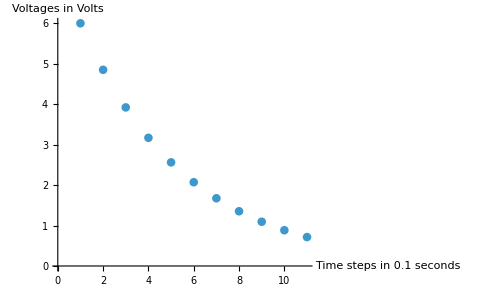

This graph might look familiar. It is called “exponential decay” and the function that goes through all the points shown is V(t)=V_0 e^(-t/RC).

## Discharging the Capacitor — Discussion

When you solve the RC discharge numerically with time steps of 0.1s, you don’t get the exact answer, but you get something pretty close, and you can improve the precision by taking the time steps smaller, like 0.01s. What I had Mathematica tabulate and plot was the exact answer.

Exponential decay shows up in radioactivity. Its close friend, exponential growth, shows up in population dynamics. If your principal in a bank account is growing thanks to compounded interest, exponential growth is also applicable.

To summarize, understanding the numerical analysis in the RC circuit gives you intuition about what a capacitor does, and how the exponential can show up in a physical situation. Finally all this pays off in unexpected understanding of equations and results in seemingly unrelated fields.